```mathematica
eta=4^al*6*(Gamma[1+al]^2/Gamma[5+2*al])*(14+20*al+9*al^2+al^3)/((3+al)*(2+al))
```

(3 2^(1+2 al) (14+20 al+9 al^2+al^3) Gamma[1+al]^2)/((2+al) (3+al) Gamma[5+2 al])

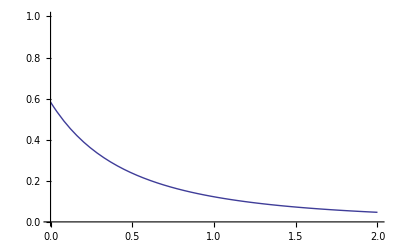

```mathematica
Plot[eta,{al,0,2},PlotRange->{0,1}]
```

```mathematica
1.0*eta//.{al->2}
```

0.0466667

```mathematica
11/180*1.0
```

0.0611111

```mathematica
(eta//.{al->2})/(11/180)
```

42/55

```mathematica
Clear[n,f]
```

```mathematica
n[ep_,al_]:=(ep)^(-al-1)
f[ep_,al_]:=(ep)^(-al)
```

```mathematica
epmin=1
sol=FullSimplify[Integrate[n[ep,al]*(eta/ep),{ep,1,Infinity}],{al>1}]/FullSimplify[Integrate[n[ep,al],{ep,1,Infinity}],{al>1}]
```

1

(3 4^al al (14+al (4+al) (5+al)) Gamma[1+al]^2)/((1+al) (2+al)^2 (3+al) Gamma[4+2 al])

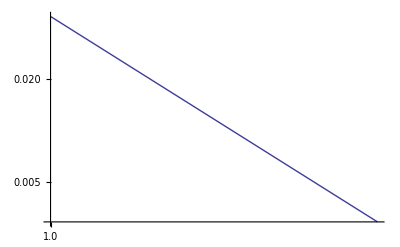

```mathematica
myal=2;
toplot=(n[ep,myal]*(eta/ep))//.{al->myal};
LogLogPlot[toplot,{ep,1,2}]
```

```mathematica
(1/2)*eta//.{al->1}
```

11/180

```mathematica
sol//.{al->1}
N[sol//.{al->1}]
(sol//.{al->1})/(11/180)
```

11/180

0.0611111

1

```mathematica
Ng=FullSimplify[Integrate[x^(-alpha),{x,ep,Infinity}],{alpha>1,ep>0}]
```

ep^(1-alpha)/(-1+alpha)

```mathematica
total=FullSimplify[Integrate[f[ep,al],{ep,emin,emax}],{emin>0,emax>emin,emax>0,al>1}]
```

((emax emin)^-al (emax^al emin-emax emin^al))/(-1+al)

```mathematica
TeXForm[Evaluate[total//.{al->alpha}]]
```

\frac{(\text{emax} \text{emin})^{-\alpha } \left(\text{emin} \text{emax}^{\alpha }-\text{emax} \text{emin}^{\alpha }\right)}{\alpha -1}

```mathematica
mysol=FullSimplify[sol//.{al->alpha-1},{alpha≥1}]
```

(3 2^(-1+2 alpha) (-1+alpha) (2+alpha (1+alpha) (5+alpha)) Gamma[alpha]^2)/(alpha (1+alpha) (2+alpha) Gamma[3+2 alpha])

```mathematica
TeXForm[mysol]
```

\frac{3 2^{2 \alpha -1} (\alpha -1) (\alpha  (\alpha +1) (\alpha +5)+2) \Gamma (\alpha )^2}{\alpha  (\alpha +1) (\alpha +2) \Gamma (2
   \alpha +3)}

```mathematica
epmin=1
sol=FullSimplify[Integrate[f[ep,al]*(eta/ep),{ep,epmin,Infinity}],{al>1}]/FullSimplify[Integrate[f[ep,al],{ep,epmin,Infinity}],{al>1}]
```

1

(3 4^al (-1+al) al (14+al (4+al) (5+al)) Gamma[al]^2)/((2+al)^2 (3+al) Gamma[4+2 al])

```mathematica
sol//.{al->2}
N[%]
N[%]*3
```

7/300

0.0233333

0.07

```mathematica
alpha=q^2/(hbar*c);
sigmat=(8*Pi/3)*(alpha*hbar/(me*c))^2;
sigmat2=(8*Pi/3)*(q^4/(me^2*c^4));
AA=(2*Pi*q^4)/(me^2*c^4)
sigmakn=(3/4)*sigmat*((1+alphakn)/(alphakn^2)*(2*(1+alphakn)/(1+2*alphakn)-1/alphakn*Log[1+2*alphakn])+1/(2*alphakn)*Log[1+2*alphakn]-(1+3*alphakn)/(1+2*alphakn)^2);
sigmaknfreq=FullSimplify[signakn//.{alphakn->(h*freqgamma)/(me*c^2)}];
Limit[sigmakn,alphakn->0]
sigmat-Limit[sigmakn,alphakn->0]
sigmat2-Limit[sigmakn,alphakn->0]
Series[sigmakn,{alphakn,Infinity,1}]
mysigmakn=FullSimplify[(sigmakn//.{alphakn->ep})/sigmat]
```

(2 π q^4)/(c^4 me^2)

(8 π q^4)/(3 c^4 me^2)

0

0

(π q^4 (1+2 Log[2]-2 Log[1/alphakn]))/(2 c^4 me^2 alphakn)+O[1/alphakn]^2

(6 ep (2+ep (1+ep) (8+ep))+3 (1+2 ep)^2 (-2+(-2+ep) ep) Log[1+2 ep])/(8 ep^3 (1+2 ep)^2)

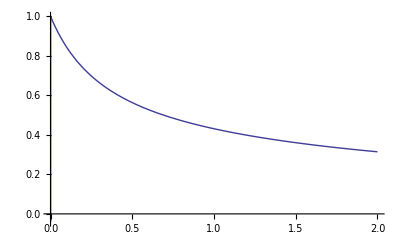

```mathematica
Plot[mysigmakn,{ep,0,2}]
```

```mathematica
TeXForm[Evaluate[mysigmakn//.{ep->epsilon}]]
```

\frac{6 \epsilon  (\epsilon  (\epsilon +1) (\epsilon +8)+2)+3 ((\epsilon -2) \epsilon -2) (2 \epsilon +1)^2 \log (2 \epsilon +1)}{8
   \epsilon ^3 (2 \epsilon +1)^2}